## Pressure-composition (P-x-y) Diagrams

### Ideal 2-Component Mixtures

Raoult’s law is used to plot the dew point curve and the bubble point curve. Raoult’s law states for a binary mixture:

P=x_1 P_1^sat+x_2 P_2^sat                    (1)

Equation (1) can be rewritten to eliminate the x_2 term.

P=x_1 P_1^sat+(1-x_1) P_2^sat      (2)

The Antoine equation is used to get the saturation pressures of each component (P_1^sat and P_2^sat).

log_10(P^sat)=A-B/(T+C)   	  (3)

In equation (3) A, B, and C are constants specific to each component.

For the bubble-point (BP) calculation ∑K_i x_i=1 is used to find the BP pressure. K_i is the K ratio of component i; according to Raoult’s law, K_i is the ratio of the component partial pressure to the total pressure K_i=P_i^sat/P.

1=P_1^sat/P x_1+P_2^sat/P x_2		(4)

Multiplying equation (4) through by P returns equation (1)

For the dew-point (DP) calculation, ∑y_i/K_i=1 is used to calculate DP pressure.

y_1 P/P_1^sat+y_2 P/P_2^sat=1		(5)

Rearranging equation (5) to solve for pressure as a function of the vapor composision of the more volatile component.

P=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)			(6)

For a detailed exlanation of Raoult’s law, please view Raoult’s Law Explanation.

#### Mapping a P-x-y Diagram

The blue line represents the bubble-point, above this line at higher pressures both components are in the liquid phase. Likewise, the green line represents the dew-point, below this line both components are in the vapor phase. Inside the shaded region between the two curves is the 2-phase region. The amount of each phase that is present at a certain composition in the 2-phase region is determined from the lever rule.

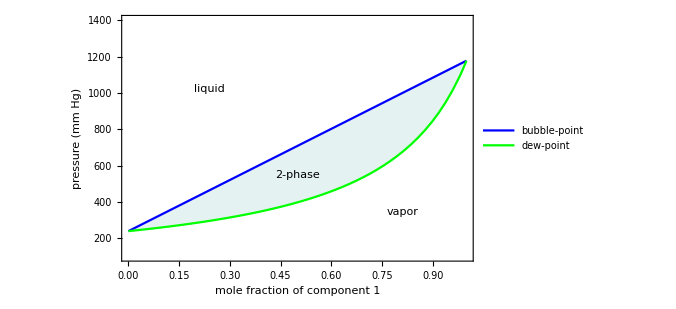

```mathematica
Module[{Psat1,Psat2,Px,Py},
Psat1=10^(6.90565-1211.033/(95+220.79)); 
Psat2=10^(6.65464-1344.8/(95+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,PlotLegends->Placed[LineLegend[{Style["bubble-point",15],Style["dew-point",15]}],Above],Filling->{1->{{2},Opacity[0.1,Blend[{Blue,Green},0.5]]}},
Epilog->{
Inset[Text@Style["liquid",18,Darker[Gray,0.4]],Scaled[{0.25,0.7}]],
Inset[Text@Style["vapor",18,Darker[Gray,0.4]],Scaled[{0.8,0.2}]],
Inset[Text@Style["2-phase",18,Darker[Gray,0.4]],Scaled[{0.5,0.35}]]
}]]
```

#### Lever Rule

The lever rule is used to determine the relative amounts of liquid and vapor in the system. An explanation of the lever rule is shown in this Screencast.
 
Mouseover the plot below to see the points used in the lever rule calculations.

	L=(y_1-z_1)/(y_1-x_1)	liquid amount present at z_1
	V=(x_1-z_1)/(x_1-y_1)	vapor amount present at z_1

```mathematica
Module[{T,p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
T=95;
p=550;
Psat1=10^(6.90565-1211.033/(T+220.79)); 
Psat2=10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.4<y1,(y1-0.4)/(y1-x1),
Px[0.4]≤p,1,
Py[0.4]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.4,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,Green,Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+40},{0.39,p+40},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+40},{(x1+0.4)/2,p+400}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+40},{y1,p+40},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+40},{(0.4+y1)/2,p+400}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],16],{(y1+0.4)/2,p+500}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],16],{(x1+0.4)/2,p+500}]
}];
p3=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,Green,Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+40},{0.39,p+40},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+40},{(x1+0.4)/2,p+400}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+40},{y1,p+40},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+40},{(0.4+y1)/2,p+400}}]},
Text[Style["L",16],{(y1+0.4)/2,p+450}],
Text[Style["V",16],{(x1+0.4)/2,p+450}],
{PointSize[0.015],Point[{x1,p}]},Text[Style["x_1",17],{x1,p},{-1,1}],
{PointSize[0.015],Point[{0.4,p}]},Text[Style["z_1",17],{0.415,p},{-1,1}],
{PointSize[0.015],Point[{y1,p}]},Text[Style["y_1",17],{y1,p},{-1,1}]
}];
Mouseover[Show[p1,p2],Show[p1,p3]]]
```

```mathematica
(*manipulate, changing composition at constant pressure to see changing amts. show maths -- liq fraction over total, etc*)
```

#### Concept Test #1 - Changing Pressure

*Effect changing the pressure at constant overall composition has on liquid/vapor amounts (lever rule), compositions in each phase, etc.

#### Effect on Liquid and Vapor Amounts

***intro, find concept test to insert (one with piston cylinder?), then demo (below) to help visualize. Can add explanaition directly to demo using mouseover.

	⟶Concept test

As pressure increases at constant composition, the binary mixture is compressed and thus goes from the vapor phase to liquid phase.

```mathematica
Manipulate[
Module[{T,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
T=95;
Psat1=10^(6.90565-1211.033/(T+220.79)); 
Psat2=10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.09],Point[{0,0}]}],{0.5,p}]];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,Green},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{120,300},ChartLabels->Placed[{Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,Bold],Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,Bold]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,Green,Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{p,530,"pressure (mm Hg)"},200,1000,5,Appearance->"Labeled"}]
```

#### Changing Pressre - Effect on Molar Composition in Each Phase

```mathematica
Manipulate[
Module[{T,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
T=95;
Psat1=10^(6.90565-1211.033/(T+220.79)); 
Psat2=10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.055],Point[{0,0}]}],{0.5,p}]];
p3=Graphics[{
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{0.310296,530},{0.5,530}}]},
{Thick,Dashed,Blend[{Green,Gray},0.65],Line[{{0.5,530},{0.688999,530}}]},
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{0.310296,530},{0.310296,100}}]},
{Thick,Dashed,Blend[{Green,Gray},0.65],Line[{{0.688999,530},{0.688999,100}}]},

{Gray,PointSize[0.02],Point[{0.5,530}]},

{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,Green,Line[{{0.5,p},{y1,p}}]},
{Thick,Dashed,Blue,Line[{{x1,p},{x1,100}}]},
{Thick,Dashed,Green,Line[{{y1,p},{y1,100}}]},
If[p==530,Text@"",
{{Thick,Arrow[{{0.310296,150},{x1,150}}]},
{Thick,Arrow[{{0.688999,150},{y1,150}}]}}]
}];
Show[p1,p3]
],
{{p,530,"pressure (mm Hg)"},400,705,5,Appearance->"Labeled"}]
```

```mathematica
(****)
```

#### Manipulating Temperature

```mathematica
Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=10^(6.90565-1211.033/(T+220.79)); 
Psat2=10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[530==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[530==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤530,1,
Py[0.5]≥530,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[
Graphics[{PointSize[0.09],Point[{0,0}]}],{0.5,530}]];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,Green},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{120,300},ChartLabels->Placed[{Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,Bold],Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,Bold]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,530},{0.5,530}}]},
{Thick,Dashed,Green,Line[{{0.5,530},{y1,530}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{T,95,"temperature (°C)"},70,100,1,Appearance->"Labeled"}]
```